# Chapter 20.

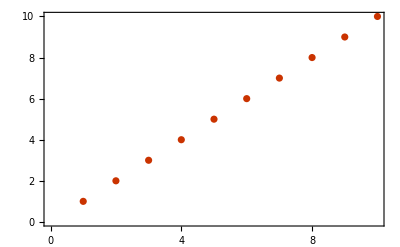

```mathematica
ListPlot[Range[10],PlotTheme->"Web"]
```

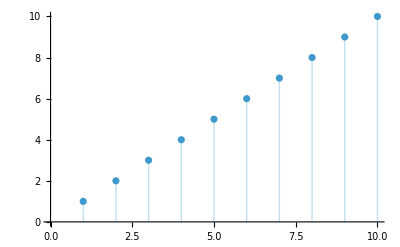

```mathematica
ListPlot[Range[10], Filling->Axis]
```

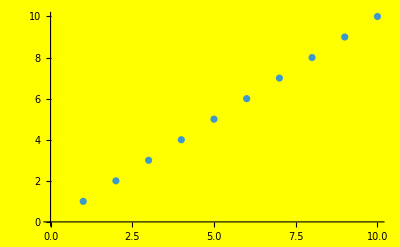

```mathematica
ListPlot[Range[10], Background->Yellow]
```

```mathematica
GeoListPlot[ Entity["Country","Australia"],GeoRange-> Entity["Planet","Earth"]]
```

-Graphics-

```mathematica
GeoListPlot[ Entity["Country","Madagascar"],GeoRange-> Entity["Ocean","IndianOcean"]]
```

-Graphics-

```mathematica
GeoGraphics[EntityClass["Country","SouthAmerica"],GeoBackground->"ReliefMap"]
```

-Graphics-

```mathematica
GeoListPlot[{Entity["Country","France"],Entity["Country","Finland"],Entity["Country","Greece"]},GeoRange->Entity["GeographicRegion","Europe"],GeoLabels->Automatic]
```

-Graphics-

```mathematica
GeoListPlot[EntityClass["University","TheIvyLeague"],GeoLabels->True]
```

-Graphics-

```mathematica
Grid[Table[Style[x*y,White],{x,12},{y,12}],Background->Black]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144


{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Disk[],ImageSize->RandomInteger[40]],100]
```

```mathematica
Table[Graphics[RegularPolygon [5],ImageSize-> 30,AspectRatio->y],{y,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Manipulate[Graphics[Circle[],ImageSize->x],{x,5,500}]
```

```mathematica
Grid[Table[RandomColor[],10,10],Frame->All]
```

RGBColor[0.6293066612844982, 0.8485697938707475, 0.18819437365224867] | RGBColor[0.8681675387214878, 0.7786567209234851, 0.9426158075812052] | RGBColor[0.7870597613219223, 0.5717306229698382, 0.7594369474136466] | RGBColor[0.8461092089495141, 0.6406254083432721, 0.33822878977615534] | RGBColor[0.7320357333532705, 0.18709372395953738, 0.9083263702105848] | RGBColor[0.9825367491632555, 0.07204921883826088, 0.5246434143043457] | RGBColor[0.7872951354457416, 0.40029631491174844, 0.5291521929916354] | RGBColor[0.425395315028712, 0.6765923402624796, 0.3450067397838119] | RGBColor[0.3883043844998111, 0.16346112888581543, 0.9152598531106333] | RGBColor[0.9546524438299808, 0.6679776292266169, 0.24710332621684383]
RGBColor[0.0354394098909836, 0.2829271070741832, 0.9778700904484894] | RGBColor[0.6344596661539452, 0.025025883112605563, 0.07520992065673116] | RGBColor[0.31783502416063425, 0.1965813272589696, 0.2179280338545626] | RGBColor[0.371862715819804, 0.981189740599866, 0.7803027777338889] | RGBColor[0.8484170303613288, 0.4679310455708152, 0.6234689038093919] | RGBColor[0.1417957987947498, 0.7547165911440903, 0.9984998297433869] | RGBColor[0.9558228888304137, 0.7125447628964074, 0.7305423155204578] | RGBColor[0.41542526199229957, 0.5231940817465701, 0.6754153100591656] | RGBColor[0.06572628682957382, 0.32254633831577517, 0.737051590672207] | RGBColor[0.4112446162537433, 0.2987553509529428, 0.6732283583587051]
RGBColor[0.23618756667424146, 0.5711025996930041, 0.9195862200333864] | RGBColor[0.5526140035826752, 0.4789873531312354, 0.4354006083934783] | RGBColor[0.07349583885019295, 0.5694866399640377, 0.9902827960547411] | RGBColor[0.7644912544520981, 0.8373669021631447, 0.33495050971927] | RGBColor[0.4322272539027354, 0.6295673487464997, 0.9541070787140573] | RGBColor[0.8371391898289784, 0.4913479851448197, 0.12712920859177834] | RGBColor[0.6523796371861965, 0.3834695197757969, 0.28206362446095157] | RGBColor[0.34070555238394706, 0.9044136016157052, 0.0081479607171695] | RGBColor[0.8386104576144173, 0.4894207696117381, 0.6650015983868625] | RGBColor[0.5325200497686762, 0.8526838078191812, 0.5490500079278671]
RGBColor[0.5352811106316699, 0.4284776534126362, 0.9042705183166986] | RGBColor[0.5040128184898411, 0.05000974608451947, 0.9372874441615004] | RGBColor[0.913783182237518, 0.5099428379672966, 0.009459641015516329] | RGBColor[0.22990669007178655, 0.5079327717540794, 0.99663817951319] | RGBColor[0.7966255061988765, 0.11534313892342052, 0.5630090193727559] | RGBColor[0.2169820575879129, 0.006045265446105841, 0.5991176689113706] | RGBColor[0.9434711314877764, 0.42156923131257096, 0.8609695601136622] | RGBColor[0.7589203256322592, 0.38601223801612217, 0.6941826967574574] | RGBColor[0.942116907907441, 0.8241327127914257, 0.9637038909954727] | RGBColor[0.563369905284324, 0.8201604156191182, 0.37091985595292476]
RGBColor[0.7692923038606836, 0.20615287777989044, 0.04942139728942996] | RGBColor[0.26705201722281524, 0.2898086688543555, 0.4197719310611294] | RGBColor[0.7739997999221493, 0.6805938286978317, 0.863056760116613] | RGBColor[0.17495281778530414, 0.24494538572462443, 0.7829960444964374] | RGBColor[0.5582910339641642, 0.3902102611181224, 0.5760060481710663] | RGBColor[0.8251674501240636, 0.43602982913152943, 0.3999220558401342] | RGBColor[0.7769755737570778, 0.2866044578528226, 0.10897327131131851] | RGBColor[0.39161167781057205, 0.5286346916868292, 0.18246695400369806] | RGBColor[0.3138389413728728, 0.34208058117950957, 0.8606163540535159] | RGBColor[0.03158309394231806, 0.2964196316227412, 0.837285647413119]
RGBColor[0.08103594640133194, 0.9275572316951677, 0.5198605042464115] | RGBColor[0.8530161707659756, 0.7781673599964838, 0.44226310732684904] | RGBColor[0.3131503716699746, 0.2110302208335253, 0.07690269842284758] | RGBColor[0.48006646120447094, 0.5142252860597354, 0.19936505538903182] | RGBColor[0.7634927781726679, 0.793385281007599, 0.7280157385926074] | RGBColor[0.7608433538730708, 0.0033312230793147712, 0.44210330846474544] | RGBColor[0.3041058014855207, 0.7365845574939647, 0.3045821736326755] | RGBColor[0.37845789842264743, 0.4608825375821046, 0.9685442048278377] | RGBColor[0.6415038253815641, 0.4252776722547995, 0.4798411002224954] | RGBColor[0.9341631513527366, 0.12531200434628165, 0.8159298765444027]
RGBColor[0.7056592230534546, 0.7471101638980238, 0.6365066673280098] | RGBColor[0.17755848143129027, 0.6287655152493901, 0.3411255561177631] | RGBColor[0.9087913345652894, 0.5927527741449596, 0.6003823812392495] | RGBColor[0.14874677768640354, 0.6543868033343512, 0.3248709207643734] | RGBColor[0.30263034179390336, 0.3656732462972465, 0.16771134119366882] | RGBColor[0.4762040826952747, 0.636624174753021, 0.05310421739839377] | RGBColor[0.7697101178477692, 0.841216506455257, 0.4568950000160974] | RGBColor[0.23760519600402952, 0.31378964054436165, 0.968613297558585] | RGBColor[0.33931043801340777, 0.9176776713377588, 0.40714574227693245] | RGBColor[0.9098268376102714, 0.4657193113026632, 0.11335686820489799]
RGBColor[0.7124002063522452, 0.6516178977642868, 0.1444900481764304] | RGBColor[0.45132719852174796, 0.617664886291917, 0.9647855525652318] | RGBColor[0.331952596285086, 0.5113926140677774, 0.21646752664720692] | RGBColor[0.01769623372117235, 0.4007590631762816, 0.5497181692871975] | RGBColor[0.004222153354656699, 0.0278611377023279, 0.31381419072316796] | RGBColor[0.9822380254096745, 0.38599604668059007, 0.5168985849692713] | RGBColor[0.45624456074345, 0.559472635980929, 0.8763260038237208] | RGBColor[0.2639102493143768, 0.2803206623274417, 0.7930978725300359] | RGBColor[0.5001648659265254, 0.9489750091209148, 0.2773573855403426] | RGBColor[0.13977282146645575, 0.42956396491067217, 0.40493284395835616]
RGBColor[0.6163124416578118, 0.8646514879027085, 0.8735813578238927] | RGBColor[0.06641557579675439, 0.36552614554275165, 0.727915516975294] | RGBColor[0.31071540977770384, 0.46908644570318603, 0.03324445057952441] | RGBColor[0.15859696711571636, 0.4857897221073959, 0.9391836091301544] | RGBColor[0.7153409625463294, 0.18059175581162612, 0.7429273043199787] | RGBColor[0.7729722910206467, 0.20938938210104063, 0.4452853297832322] | RGBColor[0.4838331580151365, 0.9215884005133788, 0.31876553205623837] | RGBColor[0.696224771115119, 0.15191029160065117, 0.29559542910974623] | RGBColor[0.1110549228835851, 0.02478827895990232, 0.8924808197918712] | RGBColor[0.2873856699456341, 0.012657756429008016, 0.6741972312089393]
RGBColor[0.08202930506156014, 0.21307381264180103, 0.356416710529335] | RGBColor[0.8668051157968379, 0.7349879801431891, 0.5074075131521825] | RGBColor[0.13141186782889624, 0.020916262018638943, 0.9399790857715005] | RGBColor[0.5430334525645006, 0.8468297669995779, 0.36029668447974195] | RGBColor[0.6495046671357072, 0.03650933607934714, 0.01960486655772198] | RGBColor[0.10662106670091887, 0.0543268065754674, 0.14071597226484456] | RGBColor[0.24587433066748843, 0.5721267273678923, 0.07491115363299117] | RGBColor[0.807081886106237, 0.46977683096330014, 0.09292101901726446] | RGBColor[0.21283713097744994, 0.875264541190572, 0.8345019001751781] | RGBColor[0.8357682404623952, 0.3111660943340189, 0.9557795861028238]

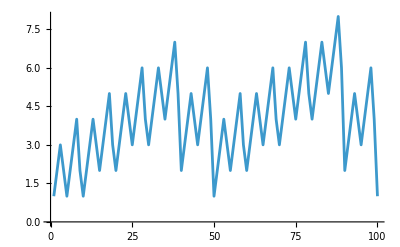

```mathematica
ListLinePlot[Table[StringLength[RomanNumeral[n]],{n,100}],PlotRange->Max[Table[StringLength[RomanNumeral[n]],{n,100}]]]
```

# Chapter 21.

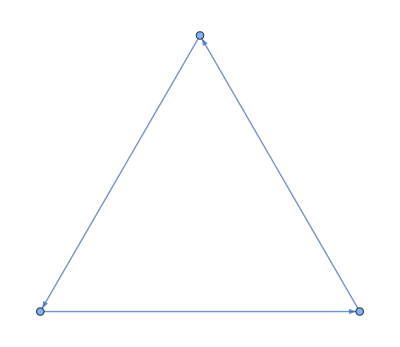

```mathematica
Graph[{1->2,2->3,3->1}]
```

```mathematica
Graph[Flatten[Table[x->y,{x,4},{y,4}]]]
```

-Graphics-

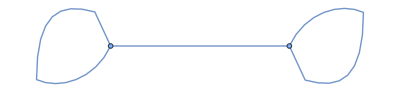
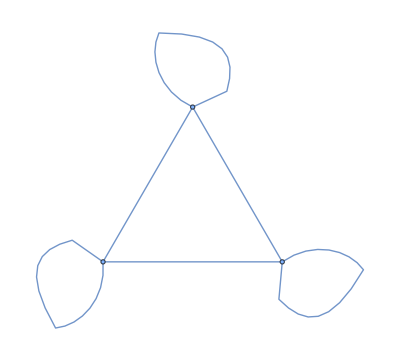
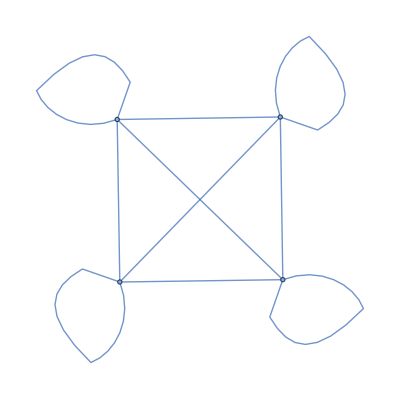
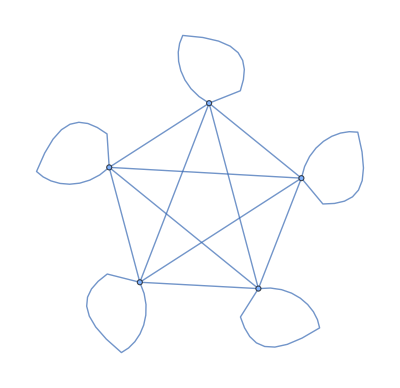
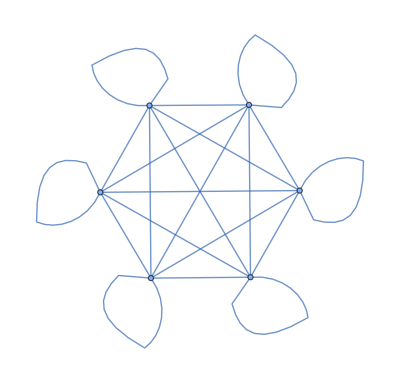
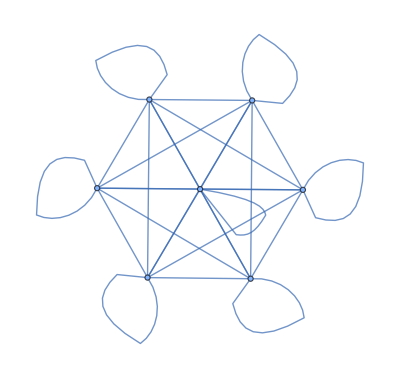
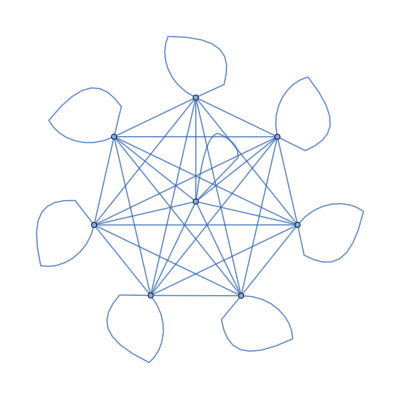
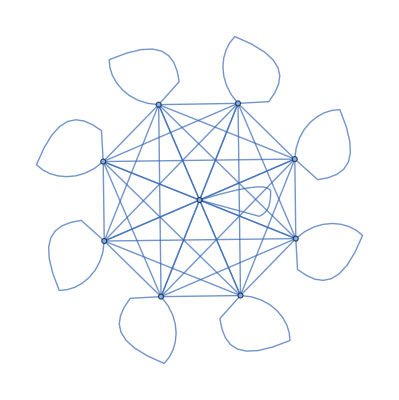

```mathematica
Table[UndirectedGraph[Flatten[Table[x->y,{x,y},{y,x}]]],{y,2,10}]
```

```mathematica
Flatten[Table[Range[2],3]]
```

{1,2,1,2,1,2}

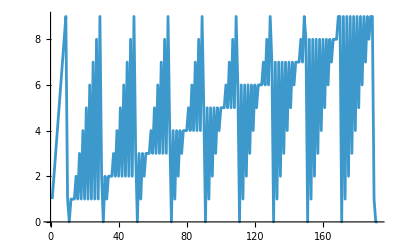

```mathematica
ListLinePlot[Flatten[Table[IntegerDigits[n],{n,100}]]]
```

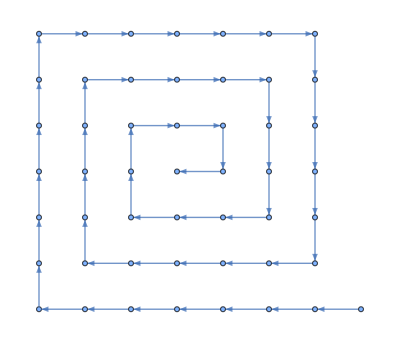

```mathematica
Graph[Table[y->y+1,{y,49}]]
```

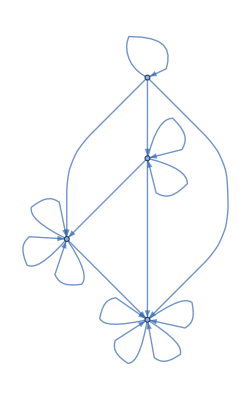

```mathematica
Graph[Flatten[Table[i->Max[i,j],{i,4},{j,4}]]]
```

```mathematica
Graph[Flatten[Table[i->j-i,{i,1,5},{j,1,5}]]]
```

-Graphics-

```mathematica
Graph[Table[i->RandomInteger[{1,100}],{i,100}]]
```

-Graphics-

```mathematica
Graph[Flatten[Table[{i->RandomInteger[{1,100}],i->RandomInteger[{1,100}]},{i,100}]]]
```

-Graphics-

```mathematica
Grid[Table[FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],x,y],{x,4},{y,4}]]
```

{1} | {1,2} | {1,2,3} | {1,2,3,4}
{2,3,1} | {2} | {2,3} | {2,3,4}
{3,1} | {3,1,2} | {3} | {3,4}
{4,1} | {4,1,2} | {4,1,2,3} | {4}

# Chapter 22.

```mathematica
LanguageIdentify["ajatella"]
```

Finnish

```mathematica
DeleteObject[ResourceObject["Wolfram ImageIdentify Net V2"]] 
ImageIdentify[Entity["TaxonomicSpecies","PantheraTigris::63rj9"][EntityProperty["TaxonomicSpecies","Image"]]]
```

tiger

```mathematica
DeleteObject[ResourceObject["Wolfram ImageIdentify Net V2"]] 
Table[ImageIdentify[Blur[Entity["TaxonomicSpecies","PantheraTigris::63rj9"][EntityProperty["TaxonomicSpecies","Image"]],x]],{x,1,5,1}]
```

{tiger,tiger,tiger,tiger,swift fox}

```mathematica
Classify["Sentiment","I'm so happy to be here"]
```

Positive

```mathematica
Nearest[WordList[],"happy",10]
```

{happy,haply,harpy,nappy,sappy,apply,campy,choppy,guppy,hairy}

```mathematica
Flatten[Table[Nearest[Table[RandomInteger[1000],20],100],3]]
```

{130,85,104}

```mathematica
Flatten[Table[Nearest[Table[RandomColor[],10],Red],5]]
```

{RGBColor[0.8222440487140068, 0.10037996424266016, 0.31536614405963026],RGBColor[0.5785740547397491, 0.2572757269646486, 0.1350719494744712],RGBColor[0.5848078804779182, 0.2989185695114953, 0.2900670629216402],RGBColor[0.7698082804826363, 0.4839202903485862, 0.54940698254212],RGBColor[0.8161782811866227, 0.851336115479677, 0.34655454187845414]}

```mathematica
Nearest[Table[x*x,{x,1,100}],2000]
```

{2025}

```mathematica
Nearest[EntityClass["Country","Europe"][EntityProperty["Country","Flag"]],Entity["Country","Brazil"][EntityProperty["Country","Flag"]],3]
```

{-Graphics-,-Graphics-,-Graphics-}

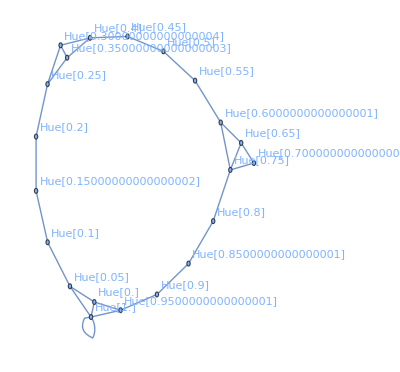

```mathematica
NearestNeighborGraph[Table[Hue[h],{h,0,1,0.05}],2,VertexLabels->Automatic]
```

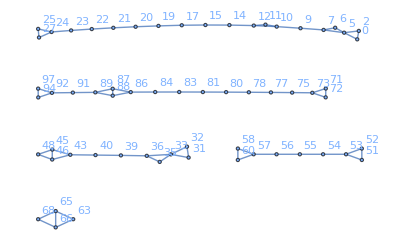

```mathematica
NearestNeighborGraph[Table[RandomInteger[100],100],2, VertexLabels->Automatic]
```


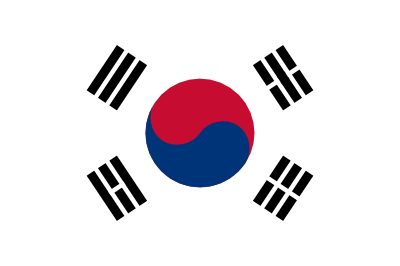
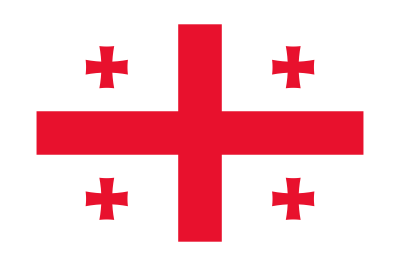
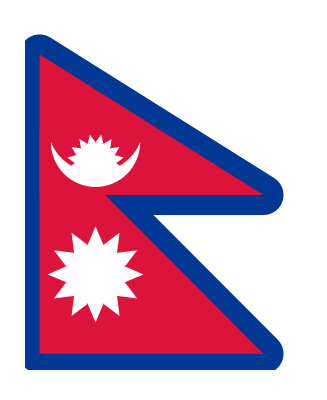
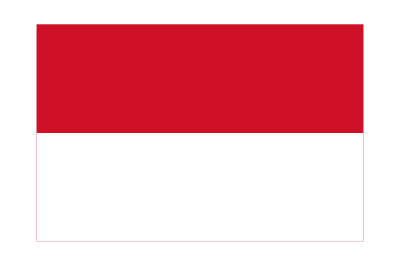
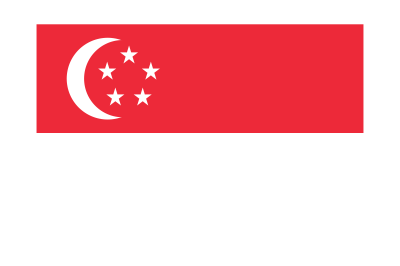
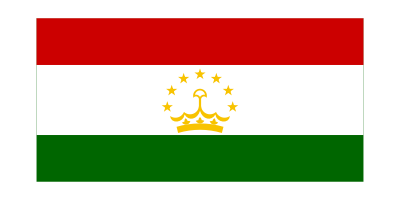
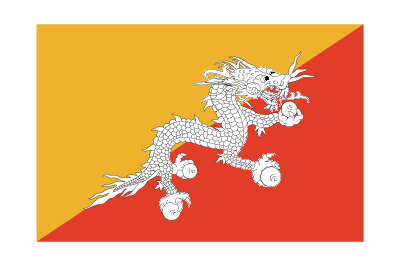
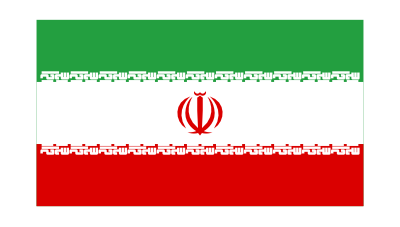

{{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
FindClusters[EntityClass["Country","Asia"][EntityProperty["Country","Flag"]]]
```

```mathematica
NearestNeighborGraph[Table[Rasterize[Style[FromLetterNumber[x],20]],{x,1,26,1}],2,VertexLabels->Automatic]
```

-Graphics-

```mathematica
Table[TextRecognize[EdgeDetect[Rasterize[Style["Programming",x]]]],{x,10,20}]
```

{Programming,Programming,P
rogramming,Programming,Programming,Programming,Programming,Programming,Programming,Programming,Programming}

```mathematica
Dendrogram[Table[Rasterize[Style[FromLetterNumber[x],10]],{x,1,10,1}]]
```

-Graphics-

```mathematica
FeatureSpacePlot[Table[Rasterize[ToUpperCase[FromLetterNumber[x]]],{x,1,26,1}]]
```

-Graphics-